# Linear Programming

R.U. Gobithaasan

## Region Plot: Linear

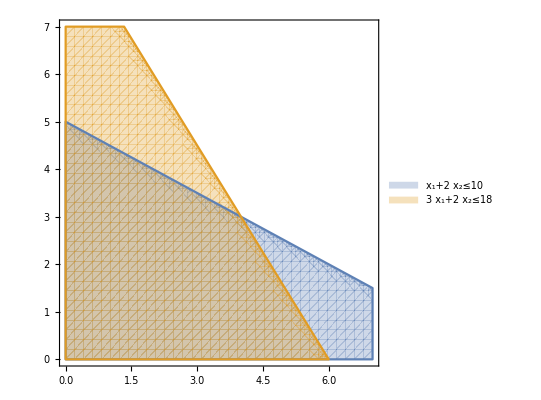
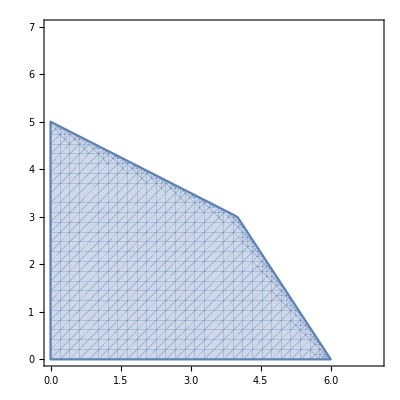

```mathematica
{RegionPlot[{Subscript[x, 1]+2 Subscript[x, 2]≤10,3 Subscript[x, 1]+2 Subscript[x, 2]≤18},{Subscript[x, 1],0,7},{Subscript[x, 2],0,7},PlotPoints->35,(*Mesh->Full,*)PlotLegends->"Expressions"] ,f1=RegionPlot[Subscript[x, 1]+2 Subscript[x, 2]≤10 &&3 Subscript[x, 1]+2 Subscript[x, 2]≤18,{Subscript[x, 1],0,7},{Subscript[x, 2],0,7},PlotPoints->35,(*Mesh->Full,*)PlotLegends->"Expressions"] (* Region INtesection*)}
```

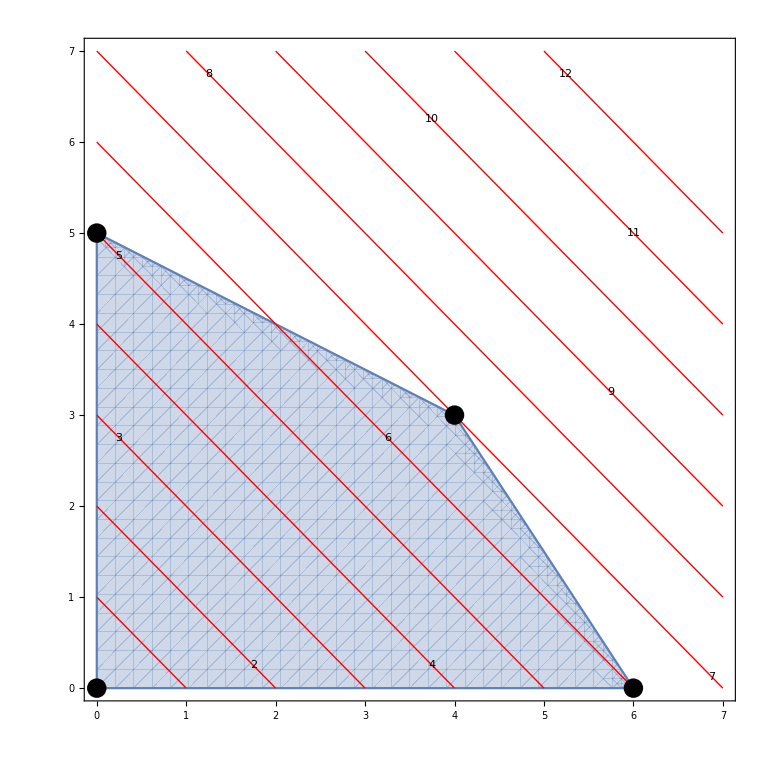

```mathematica
f2=ContourPlot[Subscript[x, 1]+Subscript[x, 2], {Subscript[x, 1],0,7},{Subscript[x, 2],0,7},ContourStyle->{Red},Contours->12,ContourShading->None,ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&)];
f3=ListPlot[{{0,0},{6,0},{4,3},{0,5}},PlotMarkers->{Automatic,Large},PlotStyle->Black];
Show[{f1,f2, f3}]
```

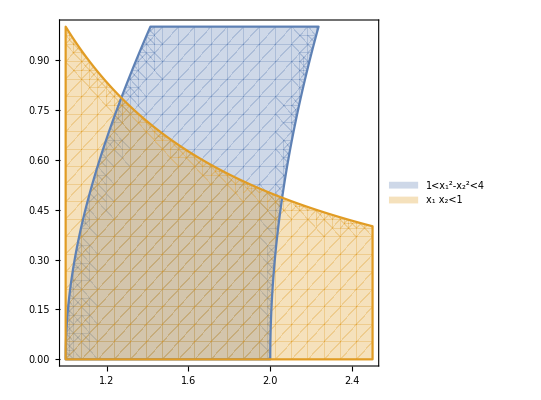
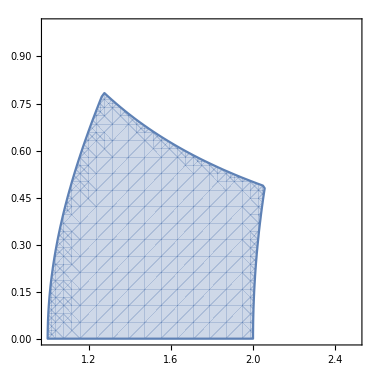

```mathematica
{RegionPlot[{1<Subscript[x, 1]^2-Subscript[x, 2]^2<4,Subscript[x, 1] Subscript[x, 2]<1},{Subscript[x, 1],1,5/2},{Subscript[x, 2],0,1},PlotLegends->"Expressions"],RegionPlot[1<x^2-y^2<4&&x y<1&&x>0&&y>0,{x,1,5/2},{y,0,1},PlotLegends->"Expressions"](*Integration*)}
```

## Nonlinear 3 Variables

```mathematica
{RegionPlot3D[{x>2y+z+3,y≤x+2z-4},{x,-2,2},{y,-2,2},{z,-2,2},Mesh->None,PlotPoints->50,PlotLegends->"Expressions"],RegionPlot3D[x>2y+z+3&&y≤x+2z-4,{x,-2,2},{y,-2,2},{z,-2,2},Mesh->None,PlotPoints->50]}
```

{-Graphics3D-,-Graphics3D-}

## Higher Dimension

```mathematica
data=Table[Insert[AngleVector[1+{2,8}*RandomReal[]],RandomReal[],2],1000];
ListPointPlot3D[data,BoxRatios->{1,1,1},PlotStyle->Directive[PointSize->Large]]
```

-Graphics3D-

```mathematica
reducer=DimensionReduction[data,2,Method->"Isomap"]
```

DimensionReducerFunction[…]

```mathematica
uv=Flatten[Table[{x,y},{x,-7,8,.05},{y,-.7,.7,.05}],1];
ListPointPlot3D[reducer[uv,"OriginalData"],BoxRatios->{1,1,1}]
```

-Graphics3D-

## Demo on inequality

```mathematica
Subscript[ineq, 1] = False;
Subscript[ineq, 2] = False;
Subscript[ineq, 3] = False;
Manipulate[RegionPlot[{
If[Subscript[ineq, 1],y>Subscript[m, 1] x + Subscript[b, 1],y<Subscript[m, 1] x + Subscript[b, 1]],
If[Subscript[ineq, 2],y>Subscript[m, 2] x + Subscript[b, 2],y<Subscript[m, 2] x + Subscript[b, 2]],
If[Subscript[ineq, 3],y>Subscript[m, 3] x + Subscript[b, 3],y<Subscript[m, 3] x + Subscript[b, 3]]},
{x,-10,10},{y,-10,10},PerformanceGoal->"Quality",Axes-> True, 
PlotLabel-> Style[Column[{
Row[{"y_1 ",If[Subscript[ineq, 1],"> ","< "],If[Subscript[m, 1]<0,"","  "],ToString[NumberForm[Subscript[m, 1],{3,2}]] ," x_1",If[Subscript[b, 1]<0," - "," + "], ToString[NumberForm[Abs[Subscript[b, 1]],{3,2}]]}],
Row[{"y_2 ",If[Subscript[ineq, 2],"> ","< "],If[Subscript[m, 2]<0,"","  "],ToString[NumberForm[Subscript[m, 2],{3,2}]] ," x_2",If[Subscript[b, 2]<0," - "," + "], ToString[NumberForm[Abs[Subscript[b, 2]],{3,2}]]}],
Row[{"y_3 ",If[Subscript[ineq, 3],"> ","< "],If[Subscript[m, 3]<0,"","  "],ToString[NumberForm[Subscript[m, 3],{3,2}]] ," x_3",If[Subscript[b, 3]<0," - "," + "], ToString[NumberForm[Abs[Subscript[b, 3]],{3,2}]]}]
}],"Label",12],ImageSize->{400,400}],
{{Subscript[m, 1],1.5,Subscript[Style["m",Italic],"1"]},-3.,3.,.01,Appearance-> "Labeled", ImageSize-> Tiny},
{{Subscript[b, 1],0.4,Subscript[Style["b",Italic],"1"]},-3.,3.,.01,Appearance-> "Labeled", ImageSize-> Tiny},
Row[{"reverse inequality ",Subscript[Style["y",Italic],"1"],Spacer[10],Checkbox[Dynamic[Subscript[ineq, 1],Initialization-> False],{False,True}]}],
Delimiter,
{{Subscript[m, 2],0.3,Subscript[Style["m",Italic],"2"]},-3.,3.,.01,Appearance-> "Labeled", ImageSize-> Tiny},
{{Subscript[b, 2],2.1,Subscript[Style["b",Italic],"2"]},-3.,3.,.01,Appearance-> "Labeled", ImageSize-> Tiny},
Row[{"reverse inequality ",Subscript[Style["y",Italic],"2"],Spacer[10],Checkbox[Dynamic[Subscript[ineq, 2],Initialization-> False],{False,True}]}],
Delimiter,
{{Subscript[m, 3],-.8,Subscript[Style["m",Italic],"3"]},-3.,3.,.01,Appearance-> "Labeled", ImageSize-> Tiny},
{{Subscript[b, 3],1.3,Subscript[Style["b",Italic],"3"]},-3.,3.,.01,Appearance-> "Labeled", ImageSize-> Tiny},
Row[{"reverse inequality ",Subscript[Style["y",Italic],"3"],Spacer[10],Checkbox[Dynamic[Subscript[ineq, 3],Initialization-> False],{False,True}]}],AutorunSequencing -> {1,2,5,6},SaveDefinitions-> True]
```

## Demo 2D: LP with 2 variables

```mathematica
slope[pt1_,pt2_]:=If[First[pt1]≠First[pt2], (Last[pt2]-Last[pt1])/(First[pt2]-First[pt1]), Null];

intersect[pt1_,pt2_,a_,b_,c_]:={pt1,pt2,If[b==0,-(-c+a First[pt2])/(a (First[pt1]-First[pt2])),If[slope[pt1,pt2]==-a/b,"Lines are parallel",(-c+a *First[pt2]+b *Last[pt2])/(-a *First[pt1]+a *First[pt2]-b*Last[pt1]+b*Last[pt2])]]};

intpts[list_,a_,b_,c_]:=Select[MapThread[intersect[#1,#2,a,b,c]&,{list, RotateLeft[list]}], Last[#]≥0&&Last[#]<1&];
```

```mathematica
Manipulate[SeedRandom[sr];
corners=Table[{10*Cos[2*Pi*k], 10*Sin[2*Pi*k]}, {k,Sort[Table[Random[],{n}]]}];
max=Max[(a*First[#]+b*Last[#])&/@corners];
min=Min[(a*First[#]+b*Last[#])&/@corners];
Column[{Text@Grid[{{Row[{"Maximum value: ",max}]},{Row[{"Minimum value: ", min}]},{If[a≠0||b≠0,Style[Row[{a,"x + ",b,"y"," = ",c}],12,Red],"No objective function"]}}],Show[If[b≠0,Plot[(-a/b)*x+(c/b),{x,-10,10}, AxesOrigin->{0,0},AspectRatio->1],If[a≠0,Graphics[{Blue, Line[{{c/a,-14},{c/a,12}}]}, PlotRange->{{-11,11},{-10,14}},Axes->True],Graphics[Text["",{0,0}]]]],Graphics[{{{PointSize[.02], Point[#]}&/@corners},{LightGray, Opacity[.5],EdgeForm[Black], Polygon[corners]}, If[(a≠0||b≠0)&&Length[intpts[corners,a,b,c]]>0,
     {Red, Thick, Line[intpts[corners,a,b,c][[All,3]]*intpts[corners,a,b,c][[All,1]]+  
                                       (1-intpts[corners,a,b,c][[All,3]])*intpts[corners,a,b,c][[All,2]]
                                         ]
    }, Text["", {0,0}]
    ]}],PlotRange->{{-11,11},{-10,14}},ImageSize->{350,450}]},Center],{{n,8,"number of corners"},3,12,1, ImageSize->Small},{{a,9,"coefficient a"},-20,20, ImageSize->Small},{{b,3,"coefficient b"},-20,20, ImageSize->Small},{{c,5,"value of obj. func."},min-10,max+10, ImageSize->Small},{{sr,123,"random seed"},1,12345,1, ImageSize->Small}, ControlPlacement->Left, SaveDefinitions->True,TrackedSymbols:>{n,a,b,c,sr},AutorunSequencing->{1,2,3,5}]
```

## Demo 3D: LP with 3 variables

```mathematica
Manipulate[
If[planes,If[obj,
Show[region1,region2,region3,options], Show[region1,region2,region3 , Plot3D[z[objfunvalue],{x,0,100},{y,0,100}, Mesh->None, PlotStyle->Green, ClippingStyle->None,PerformanceGoal->"Quality"],options]],If[obj,Show[feasibleregion, options], Show[feasibleregion, Plot3D[z[objfunvalue],{x,0,100},{y,0,100}, Mesh->None, PlotStyle->Green,ClippingStyle->None],options]  ]], 
{{planes,True,"show planes"},{True,False}}, {{obj,False,"hide objective function plane"},{True, False}},{{objfunvalue,200,"objective function value"},80,240,10,Appearance->"Labeled"},Initialization:>(
options={AxesLabel->{Style["x",Italic], Style["y",Italic], Style["z",Italic]}, BoxRatios->Automatic,SphericalRegion->True, ViewPoint->{-0.9, -1.1, 0}, PlotRange->{{0,100},{0,100},{0,100}},ImageSize->{450,400},PlotRangePadding->Scaled[0.02]};region1 = Plot3D[500/9 - x/3 -5y/9, {x,0,100}, {y,0,100}, PlotStyle->LightBlue, Lighting->"Neutral", ClippingStyle->None,Evaluate@options];region2 = Plot3D[70 - 4x/5 , {x,0,100}, {y,0,100}, PlotStyle->Orange, Lighting->"Neutral", ClippingStyle->None,Evaluate@options];region3 = Plot3D[50 -2y/3, {x,0,100}, {y,0,100},PlotStyle->Purple, Lighting->"Neutral", ClippingStyle->None,Evaluate@options];
z[t_] := t/3 - 2x/3 - y/2;feasibleregion = RegionPlot3D[3x + 5y + 9z≤ 500 && 4x + 5z ≤ 350 && 2y + 3z ≤ 150, {x,0,100},{y,0,100}, {z, 0, 100}, Mesh->None,PlotStyle->Directive[Opacity[0.5],Red], Evaluate@options];
)]
```

## Solution: simplex approach

```mathematica
{RegionPlot[{Subscript[x, 1]+2 Subscript[x, 2]≤10,3 Subscript[x, 1]+2 Subscript[x, 2]≤18},{Subscript[x, 1],0,7},{Subscript[x, 2],0,7},PlotPoints->35,(*Mesh->Full,*)PlotLegends->"Expressions"] ,f1=RegionPlot[Subscript[x, 1]+2 Subscript[x, 2]≤10 &&3 Subscript[x, 1]+2 Subscript[x, 2]≤18,{Subscript[x, 1],0,7},{Subscript[x, 2],0,7},PlotPoints->35,(*Mesh->Full,*)PlotLegends->"Expressions"] (* Region INtesection*)}
```

{-Graphics-,-Graphics-}

LinearProgrammingpaclet:ref/LinearProgramming[c,m,b,{l_1,l_2,…}]
minimizes c.x subject to the constraints specified by m and b and x_i≥l_i.

```mathematica
LinearProgramming[{1,1},{{1,2},{3,2}},{10,18},{0,0},Method->"Simplex"]
```

{4,3}

Minimize x+y, 
subject to constraint
 x+2 y≥3,
  x≥-1,
   y≥-1:

## Matrics Row reduce: Gauss Elimination

```mathematica
a={{1,2,3},{4,5,6},{7,8,9}};
MatrixForm[a]
RowReduce[a]//MatrixForm
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
({{1, 0, -1}, {0, 1, 2}, {0, 0, 0}})
```

## Example in the book:

## 3.17 = 3.21

```mathematica
ClearAll["Global`*"]
```

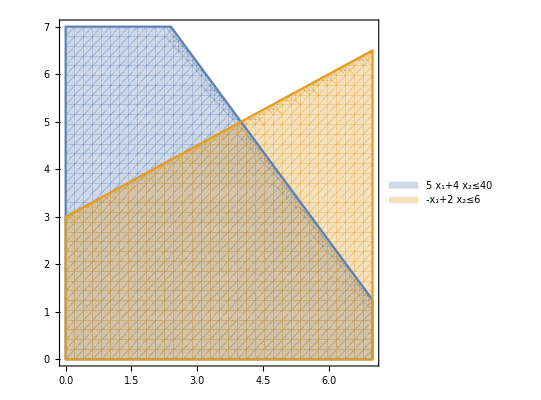
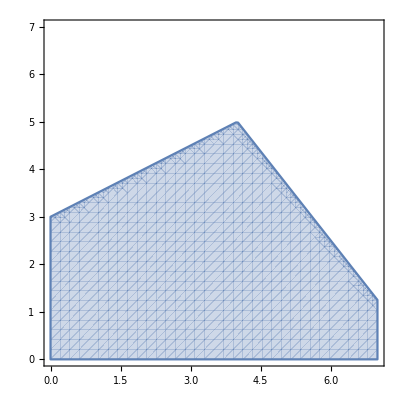

```mathematica
{f0=RegionPlot[{5 Subscript[x, 1]+4 Subscript[x, 2]≤40,-Subscript[x, 1]+2 Subscript[x, 2]≤6},{Subscript[x, 1],0,7},{Subscript[x, 2],0,7},PlotPoints->35,(*Mesh->Full,*)PlotLegends->"Expressions"] ,f1=RegionPlot[5 Subscript[x, 1]+4 Subscript[x, 2]≤40&&-Subscript[x, 1]+2 Subscript[x, 2]≤6,{Subscript[x, 1],0,7},{Subscript[x, 2],0,7},PlotPoints->35,(*Mesh->Full,*)PlotLegends->"Expressions"] (* Region INtesection*)}
```

```mathematica
f2=ContourPlot[Subscript[x, 1]+4 Subscript[x, 2], {Subscript[x, 1],0,7},{Subscript[x, 2],0,7},ContourStyle->{Red},Contours->12,ContourShading->None,ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&)];
```

{4,5}

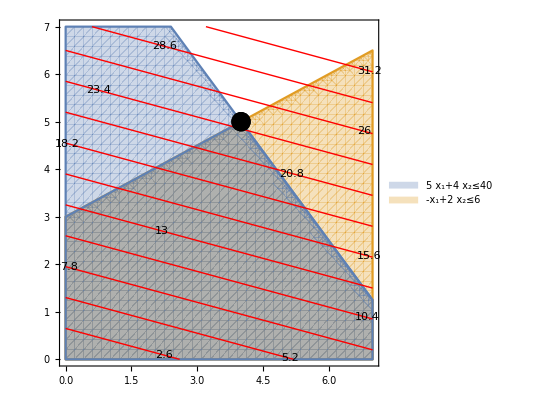

```mathematica
sol=LinearProgramming[{1,4},{{-1,2},{5,4}},{6,40},{0,0},Method->"Simplex"]
f3=ListPlot[{sol},PlotMarkers->{Automatic,Large},PlotStyle->Black];
Show[{f0,f1,f2,f3}]
```

## 3.18

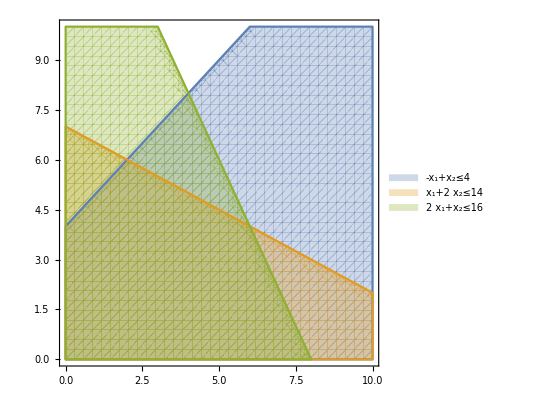
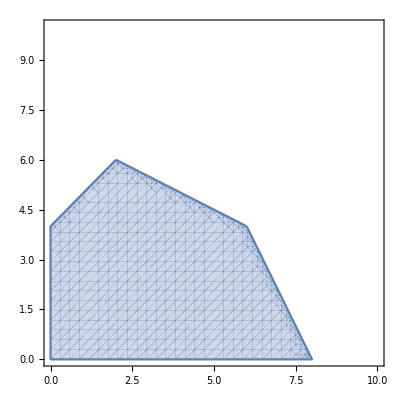

```mathematica
ClearAll["Global`*"]
{f0=RegionPlot[{-Subscript[x, 1]+Subscript[x, 2]≤4,Subscript[x, 1]+2 Subscript[x, 2]≤14, 2 Subscript[x, 1]+Subscript[x, 2]≤16},{Subscript[x, 1],0,10},{Subscript[x, 2],0,10},PlotPoints->35,(*Mesh->Full,*)PlotLegends->"Expressions"] ,f1=RegionPlot[-Subscript[x, 1]+Subscript[x, 2]≤4 && Subscript[x, 1]+2 Subscript[x, 2]≤14 && 2 Subscript[x, 1]+Subscript[x, 2]≤16,{Subscript[x, 1],0,10},{Subscript[x, 2],0,10},PlotPoints->35,(*Mesh->Full,*)PlotLegends->"Expressions"] (* Region INtesection*)}
```

```mathematica
f2=ContourPlot[4 Subscript[x, 1]+3 Subscript[x, 2], {Subscript[x, 1],0,10},{Subscript[x, 2],0,10},ContourStyle->{Red},Contours->12,ContourShading->None,ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&)];
```

{36,{x_1→6,x_2→4}}

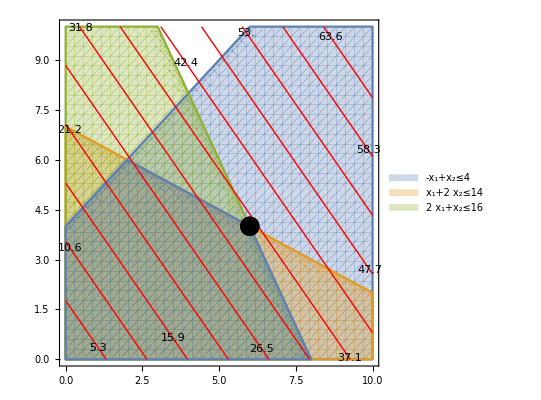

```mathematica
(*solLP=LinearProgramming[{4,3},{{-1,1},{1,2},{2,1}},{4,14,16},{0,0},Method->"Simplex"]*)
(*f3=ListPlot[{solLP},PlotMarkers->{Automatic,Large},PlotStyle->Black];*)
{m,rules}=Maximize[{4 Subscript[x, 1]+3 Subscript[x, 2],-Subscript[x, 1]+Subscript[x, 2]≤4,Subscript[x, 1]+2 Subscript[x, 2]≤14, 2 Subscript[x, 1]+Subscript[x, 2]≤16},{Subscript[x, 1],Subscript[x, 2]}]
f4=ListPlot[{{Subscript[x, 1],Subscript[x, 2]}}/.rules,PlotMarkers->{Automatic,Large},PlotStyle->Black];
{(*Show[{f0,f1,f2,f3}],*)Show[{f0,f1,f2,f4}]}
```

## 3.19

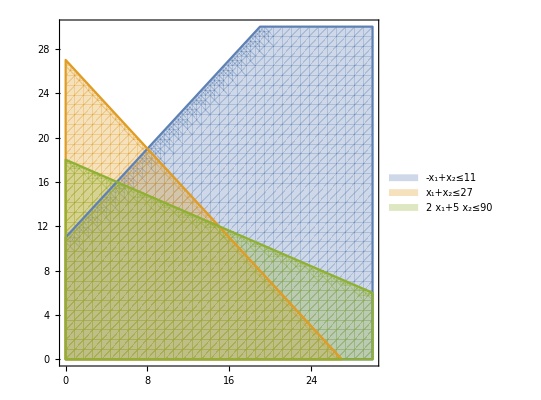
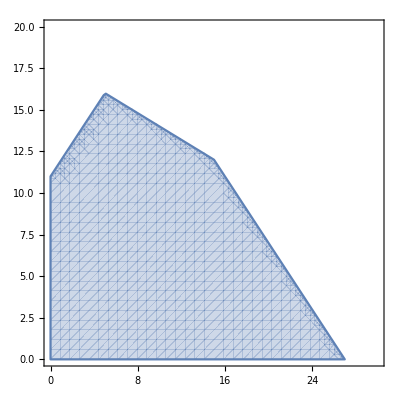

```mathematica
ClearAll["Global`*"]
{f0=RegionPlot[{-Subscript[x, 1]+Subscript[x, 2]≤11,Subscript[x, 1]+Subscript[x, 2]≤27, 2 Subscript[x, 1]+5 Subscript[x, 2]≤90},{Subscript[x, 1],0,30},{Subscript[x, 2],0,30},PlotPoints->35,(*Mesh->Full,*)PlotLegends->"Expressions"] ,f1=RegionPlot[-Subscript[x, 1]+Subscript[x, 2]≤11&&Subscript[x, 1]+Subscript[x, 2]≤27&&
 2 Subscript[x, 1]+5 Subscript[x, 2]≤90,{Subscript[x, 1],0,30},{Subscript[x, 2],0,20},PlotPoints->35,(*Mesh->Full,*)PlotLegends->"Expressions"] (* Region INtesection*)}
f2=ContourPlot[4 Subscript[x, 1]+6 Subscript[x, 2], {Subscript[x, 1],0,30},{Subscript[x, 2],0,30},ContourStyle->{Red},Contours->12,ContourShading->None,ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&)];
```

```mathematica
|
```

{132,{x_1→15,x_2→12}}

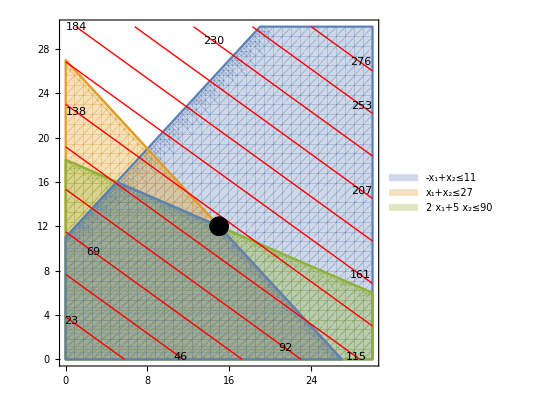

```mathematica
(*solLP=LinearProgramming[{4,6},{{-1,1},{1,1},{2,5}},{11,27,90},{0,0},Method->"Simplex"]
f3=ListPlot[{solLP},PlotMarkers->{Automatic,Large},PlotStyle->Black];*)
{m,rules}=Maximize[{4 Subscript[x, 1]+6 Subscript[x, 2],-Subscript[x, 1]+Subscript[x, 2]≤11,Subscript[x, 1]+Subscript[x, 2]≤27, 2 Subscript[x, 1]+5 Subscript[x, 2]≤90},{Subscript[x, 1],Subscript[x, 2]}]
f4=ListPlot[{{Subscript[x, 1],Subscript[x, 2]}}/.rules,PlotMarkers->{Automatic,Large},PlotStyle->Black];
{(*Show[{f0,f1,f2,f3}],*)Show[{f0,f1,f2,f4}]}
```

## 3.20

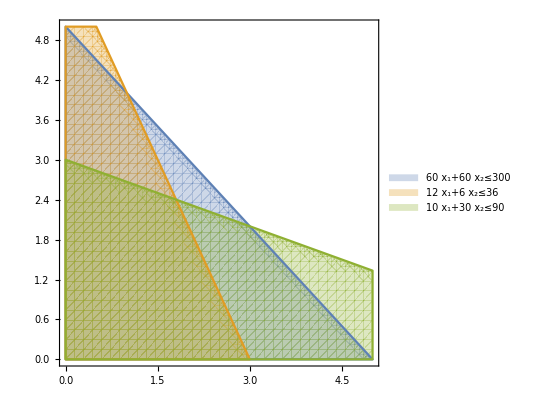
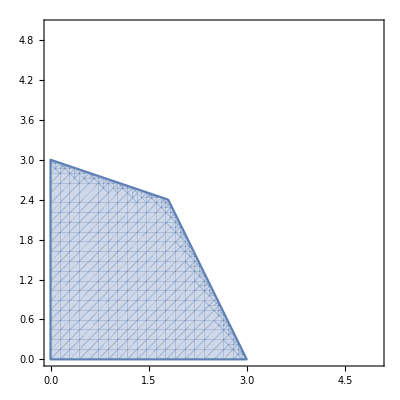

```mathematica
ClearAll["Global`*"]
{f0=RegionPlot[{60 Subscript[x, 1]+60 Subscript[x, 2]≤300,12 Subscript[x, 1]+6 Subscript[x, 2]≤36, 10 Subscript[x, 1]+30 Subscript[x, 2]≤90},{Subscript[x, 1],0,5},{Subscript[x, 2],0,5},PlotPoints->35,(*Mesh->Full,*)PlotLegends->"Expressions"] ,
f1=RegionPlot[60 Subscript[x, 1]+60 Subscript[x, 2]≤300&&12 Subscript[x, 1]+6 Subscript[x, 2]≤36&& 10 Subscript[x, 1]+30 Subscript[x, 2]≤90,{Subscript[x, 1],0,5},{Subscript[x, 2],0,5},
PlotPoints->35,(*Mesh->Full,*)PlotLegends->"Expressions"] (* Region INtesection*)}
f2=ContourPlot[0.12 Subscript[x, 1]+0.15 Subscript[x, 2], {Subscript[x, 1],0,5},{Subscript[x, 2],0,5},ContourStyle->{Red},Contours->12,ContourShading->None,ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&)];
```

{0.576,{x_1→1.8,x_2→2.4}}

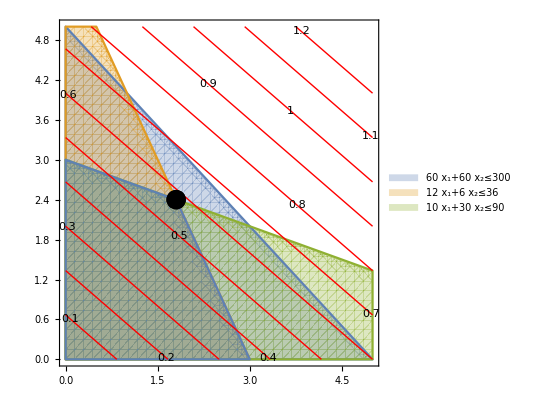

```mathematica
(*solLP=LinearProgramming[{0.12,0.15},{{60,60},{12,6},{6,36}},{300,36,90},{0,0},Method->"Simplex"]
f3=ListPlot[{solLP},PlotMarkers->{Automatic,Large},PlotStyle->Black];*)
{m,rules}=Maximize[{0.12 Subscript[x, 1]+0.15 Subscript[x, 2],60 Subscript[x, 1]+60 Subscript[x, 2]≤300,12 Subscript[x, 1]+6 Subscript[x, 2]≤36, 10 Subscript[x, 1]+30 Subscript[x, 2]≤90},{Subscript[x, 1],Subscript[x, 2]}]
f4=ListPlot[{{Subscript[x, 1],Subscript[x, 2]}}/.rules,PlotMarkers->{Automatic,Large},PlotStyle->Black];
{(*Show[{f0,f1,f2,f3}],*)Show[{f0,f1,f2,f4}]}
```

## 3.25

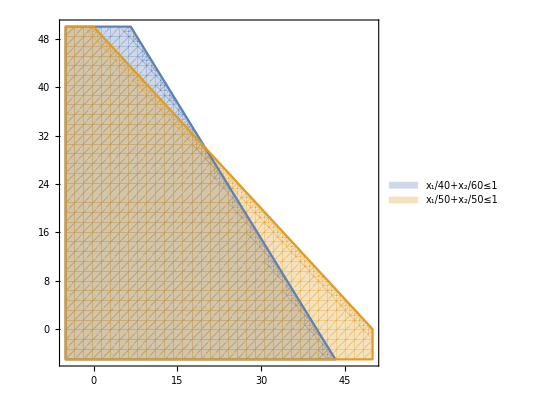
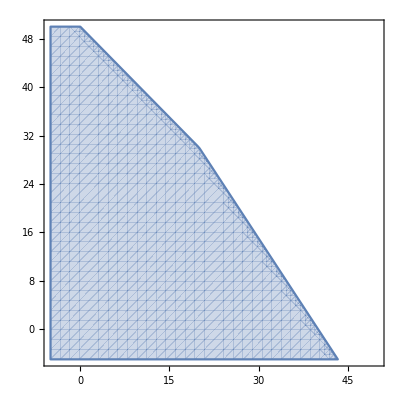

```mathematica
ClearAll["Global`*"]
{f0=RegionPlot[{1/40 Subscript[x, 1]+1/60 Subscript[x, 2]≤1,1/50 Subscript[x, 1]+1/50 Subscript[x, 2]≤1},{Subscript[x, 1],-5,50},{Subscript[x, 2],-5,50},PlotPoints->35,(*Mesh->Full,*)PlotLegends->"Expressions"] ,
f1=RegionPlot[1/40 Subscript[x, 1]+1/60 Subscript[x, 2]≤1&&1/50 Subscript[x, 1]+1/50 Subscript[x, 2]≤1,{Subscript[x, 1],-5,50},{Subscript[x, 2],-5,50},
PlotPoints->35,(*Mesh->Full,*)PlotLegends->"Expressions"] (* Region INtesection*)}
f2=ContourPlot[3 Subscript[x, 1]+2 Subscript[x, 2], {Subscript[x, 1],-5,50},{Subscript[x, 2],-5,50},ContourStyle->{Red},Contours->12,ContourShading->None,ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&)];
```

{120,{x_1→40,x_2→0}}

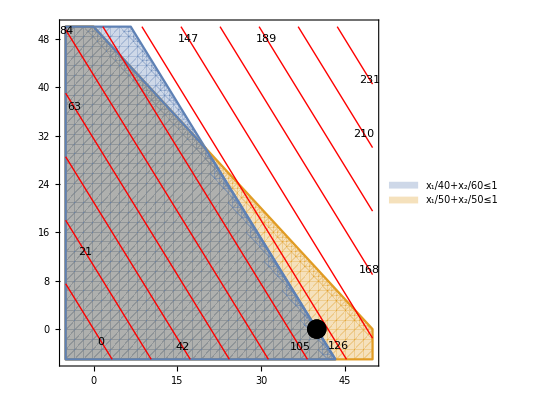

```mathematica
(*solLP=LinearProgramming[{3,2},{{1/40,1/60},{1/50,1/50}},{1,1},{0,0},Method->"Simplex"]
f3=ListPlot[{solLP},PlotMarkers->{Automatic,Large},PlotStyle->Black];*)
{m,rules}=Maximize[{03 Subscript[x, 1]+2 Subscript[x, 2],1/40 Subscript[x, 1]+1/60 Subscript[x, 2]≤1,1/50 Subscript[x, 1]+1/50 Subscript[x, 2]≤1},{Subscript[x, 1],Subscript[x, 2]}]
f4=ListPlot[{{Subscript[x, 1],Subscript[x, 2]}}/.rules,PlotMarkers->{Automatic,Large},PlotStyle->Black];
{(*Show[{f0,f1,f2,f3}],*)Show[{f0,f1,f2,f4}]}
```

## 3.26

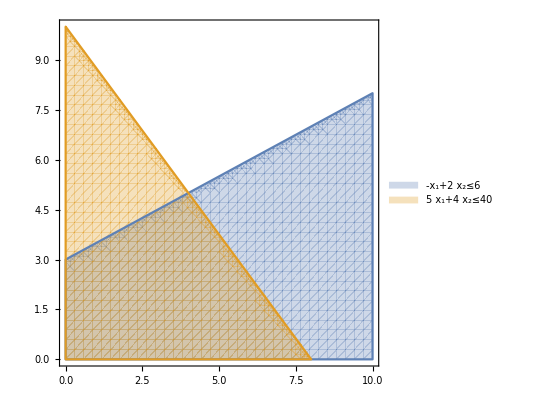
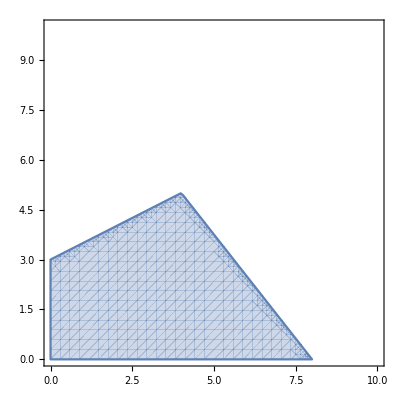

```mathematica
ClearAll["Global`*"]
{f0=RegionPlot[{-Subscript[x, 1]+2 Subscript[x, 2]≤6,5 Subscript[x, 1]+4 Subscript[x, 2]≤40},{Subscript[x, 1],0,10},{Subscript[x, 2],0,10},PlotPoints->35,(*Mesh->Full,*)PlotLegends->"Expressions"] ,
f1=RegionPlot[0-Subscript[x, 1]+2 Subscript[x, 2]≤6&&5 Subscript[x, 1]+4 Subscript[x, 2]≤40,{Subscript[x, 1],0,10},{Subscript[x, 2],0,10},
PlotPoints->35,(*Mesh->Full,*)PlotLegends->"Expressions"] (* Region INtesection*)}
f2=ContourPlot[Subscript[x, 1]+4 Subscript[x, 2], {Subscript[x, 1],0,10},{Subscript[x, 2],0,10},ContourStyle->{Red},Contours->12,ContourShading->None,ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&)];
```

{24,{x_1→4,x_2→5}}

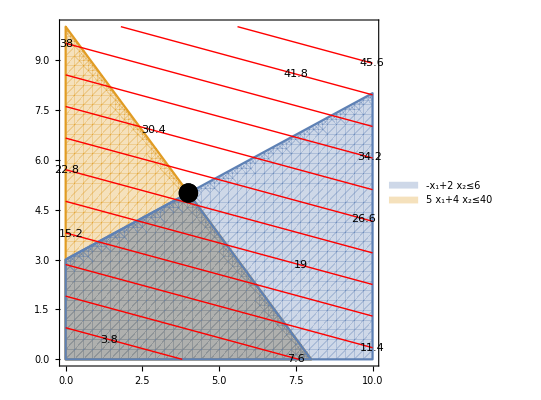

```mathematica
(*solLP=LinearProgramming[{1,4},{{-1,2},{5,4}},{6,40},{0,0},Method->"Simplex"]
f3=ListPlot[{solLP},PlotMarkers->{Automatic,Large},PlotStyle->Black];*)
{m,rules}=Maximize[{Subscript[x, 1]+4 Subscript[x, 2],-Subscript[x, 1]+2 Subscript[x, 2]≤6,5 Subscript[x, 1]+4 Subscript[x, 2]≤40},{Subscript[x, 1],Subscript[x, 2]}]
f4=ListPlot[{{Subscript[x, 1],Subscript[x, 2]}}/.rules,PlotMarkers->{Automatic,Large},PlotStyle->Black];
{(*Show[{f0,f1,f2,f3}],*)Show[{f0,f1,f2,f4}]}
```

## 3.27

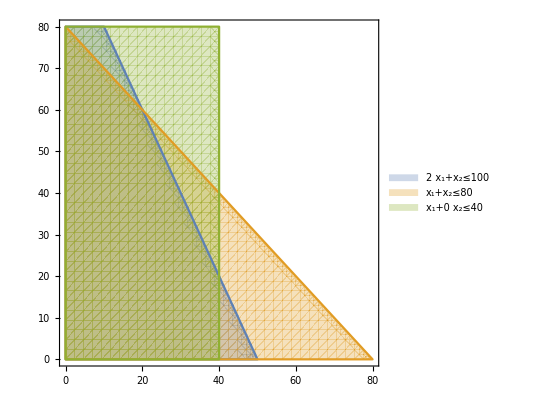
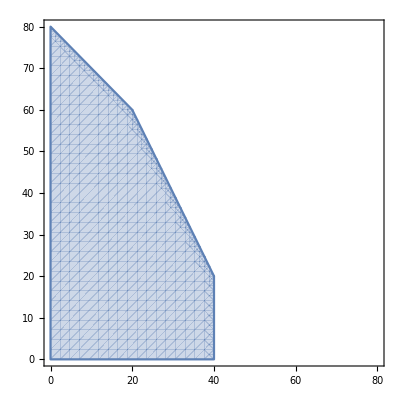

```mathematica
ClearAll["Global`*"]
{f0=RegionPlot[{2 Subscript[x, 1]+Subscript[x, 2]≤100,Subscript[x, 1]+Subscript[x, 2]≤80, Subscript[x, 1]+0*Subscript[x, 2]≤40},{Subscript[x, 1],0,80},{Subscript[x, 2],0,80},PlotPoints->35,(*Mesh->Full,*)PlotLegends->"Expressions"] ,
f1=RegionPlot[2 Subscript[x, 1]+Subscript[x, 2]≤100&&Subscript[x, 1]+Subscript[x, 2]≤80&& Subscript[x, 1]+0*Subscript[x, 2]≤40,{Subscript[x, 1],0,80},{Subscript[x, 2],0,80},
PlotPoints->35,(*Mesh->Full,*)PlotLegends->"Expressions"] (* Region INtesection*)}
f2=ContourPlot[3 Subscript[x, 1]+2 Subscript[x, 2], {Subscript[x, 1],0,80},{Subscript[x, 2],0,80},ContourStyle->{Red},Contours->15,ContourShading->None,ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&)];
```

{180,{x_1→20,x_2→60}}

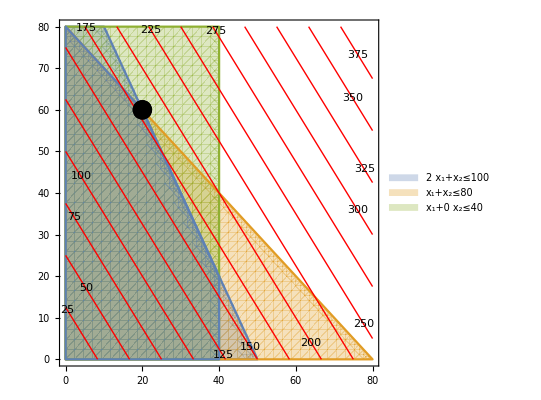

```mathematica
(*solLP=LinearProgramming[{3,2},{{2,1},{1,1},{1,0}},{100,80,40},{0,0},Method->"Simplex"]
f3=ListPlot[{solLP},PlotMarkers->{Automatic,Large},PlotStyle->Black];*)
{m,rules}=Maximize[{3 Subscript[x, 1]+2 Subscript[x, 2],2 Subscript[x, 1]+Subscript[x, 2]≤100,Subscript[x, 1]+Subscript[x, 2]≤80, Subscript[x, 1]+0*Subscript[x, 2]≤40},{Subscript[x, 1],Subscript[x, 2]}]
f4=ListPlot[{{Subscript[x, 1],Subscript[x, 2]}}/.rules,PlotMarkers->{Automatic,Large},PlotStyle->Black];
{(*Show[{f0,f1,f2,f3}],*)Show[{f0,f1,f2,f4}]}
```